```mathematica
(*lu 163 *)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
BE2outinTh={0.29,0.26,0.24,0.22,0.20,0.18,0.17,0.15,0.14};
BE2outinExp={0.21,0.22,0.21,0.22,0.21,0.21,0.26,0.30,0.30};
errorbarsBE2outin={0.11,0.02,0.02,0.02,0.03,0.02,0.05,0.09,0.11};
spins=Table[i/2,{i,31,63,4}];
p1=ListPlot[{Table[{spins[[i]],Around[BE2outinExp[[i]],errorbarsBE2outin[[i]]]},{i,1,Length[BE2outinExp]}],Table[{spins[[i]],BE2outinTh[[i]]},{i,1,Length[BE2outinTh]}]},Joined->{False, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotRange->All,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},ImageSize->350,FrameLabel->{"I [ℏ]","B(E2)_out/B(E2)_in"},PlotLegends->Placed[{"Exp","Th"},{0.3,0.2}],FrameTicks->{{Automatic,None},{{35/2,43/2,51/2,59/2},None}}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/BE2inout-1.pdf",p1];
```

```mathematica
(*lu 165 *)
ClearAll["Global`*"]
```

```mathematica
BE2outinTh={0.12,0.11,0.10};
BE2outinExp={0.17,0.16,0.22};
errorbarsBE2outin={0.05,0.03,0.08};
spins=Table[i/2,{i,39,47,4}];
p1=ListPlot[{Table[{spins[[i]],Around[BE2outinExp[[i]],errorbarsBE2outin[[i]]]},{i,1,Length[BE2outinExp]}],Table[{spins[[i]],BE2outinTh[[i]]},{i,1,Length[BE2outinTh]}]},Joined->{False, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotRange->All,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},ImageSize->350,FrameLabel->{"I [ℏ]","B(E2)_out/B(E2)_in"},PlotLegends->Placed[{"Exp","Th"},{0.3,0.8}],FrameTicks->{{Automatic,None},{{39/2,43/2,47/2},None}}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/BE2inout-2.pdf",p1];
```

```mathematica
(*lu 167 *)
ClearAll["Global`*"]
```

```mathematica
BE2outinTh={0.24,0.21,0.19};
BE2outinExp={0.23,0.26,0.27};
errorbarsBE2outinPlus={0.02,0.03,0.02};
errorbarsBE2outinMinus={0.05,0.04,0.10};
spins=Table[i/2,{i,39,47,4}];
p1=ListPlot[{Table[{spins[[i]],Around[BE2outinExp[[i]],{errorbarsBE2outinMinus[[i]],errorbarsBE2outinPlus[[i]]}]},{i,1,Length[BE2outinExp]}],Table[{spins[[i]],BE2outinTh[[i]]},{i,1,Length[BE2outinTh]}]},Joined->{False, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotRange->All,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},ImageSize->350,FrameLabel->{"I [ℏ]","B(E2)_out/B(E2)_in"},PlotLegends->Placed[{"Exp","Th"},{0.3,0.2}],FrameTicks->{{Automatic,None},{{39/2,43/2,47/2},None}}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/BE2inout-3.pdf",p1];
```

## B(M1)/B(E2)_in ratio

```mathematica
ClearAll["Global`*"]
```

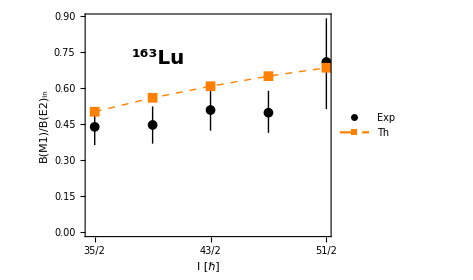

```mathematica
BM1E2exp={0.439,0.447,0.509,0.498,0.709};
BM1E2th={0.502,0.560,0.608,0.650,0.685};
errPlus={0.082,0.077,0.088,0.091,0.182};
errMinus={0.076,0.078,0.086,0.084,0.196};
spins=Table[i/2,{i,35,51,4}];
p1=ListPlot[{Table[{spins[[i]],Around[BM1E2exp[[i]],{errMinus[[i]],errPlus[[i]]}]},{i,1,Length[BM1E2exp]}],Table[{spins[[i]],BM1E2th[[i]]},{i,1,Length[BM1E2th]}]},Joined->{False, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotRange->All,PlotStyle->{{Black,Thick},{Orange,Dashed,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},ImageSize->350,FrameLabel->{"I [ℏ]","B(M1)/B(E2)_in"},PlotLegends->Placed[{"Exp","Th"},{0.3,0.2}],FrameTicks->{{Automatic,None},{{35/2,43/2,51/2},None}},Epilog->{ Inset[Style[Row[{Superscript["",163],"Lu"}],Bold,20,Black,FontFamily->"Times"],Scaled[{0.3,0.8}]]}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Quadrupole-Moments/BE2inout-4.pdf",p1];
p1
```